# GK

## viscosity

### p_0=3.825 ,T=0.0025

```mathematica
testData3825=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00250000_waitingTime10000_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

```mathematica
sacfInterp3825=Table[Interpolation[Transpose[{Normal[testData3825[[i,2]]],Normal[testData3825[[i,1]]]}],Method->"Spline"],{i,10}];
```

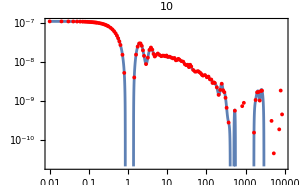
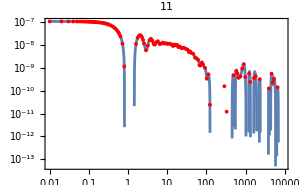
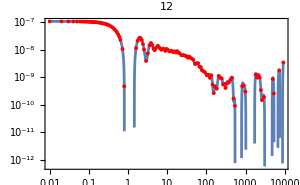
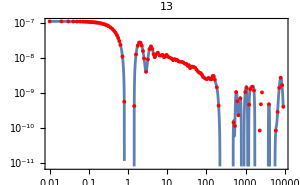
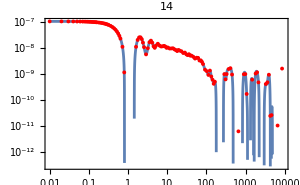
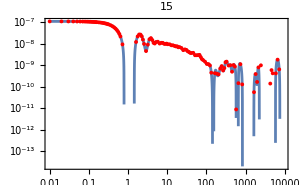
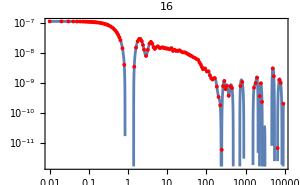
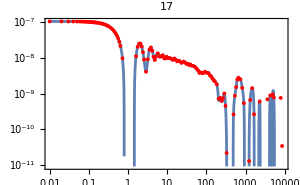

```mathematica
Table[Show[LogLogPlot[sacfInterp3825[[id]][x],{x,0.01,Last[testData3825[[id,2]]]},ImageSize->300,PlotLabel->ToString[id+9]],ListLogLogPlot[Table[{testData3825[[id,2,i]],testData3825[[id,1,i]]},{i,Length[testData3825[[id,1]]]}],PlotStyle->Red]],{id,Length[testData3825]}]
```

```mathematica
cutoff3825={370,120,150,200,150,130,250,200,200,290};
```

```mathematica
viscosity3825=Table[NIntegrate[sacfInterp3825[[i]][x],{x,0,cutoff3825[[i]]}],{i,10}]*4096/0.0025
```

{2.19131,0.837302,0.90464,1.37316,1.01182,0.809538,1.52704,1.47446,1.57014,1.31538}

```mathematica
Mean[viscosity3825]
```

1.30148

```mathematica
StandardDeviation[viscosity3825]/Sqrt[10]
```

0.135358

### p_0=3.825 ,T=0.0020

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00200000_waitingTime10000_idx12.nc"]
```

{/firstValue,/secondValue}

```mathematica
sac3825=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00200000_waitingTime10000_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

```mathematica
sacfInterpSAC3825=Table[Interpolation[Transpose[{Normal[sac3825[[i,2]]],Normal[sac3825[[i,1]]]}],Method->"Spline"],{i,10}];
```

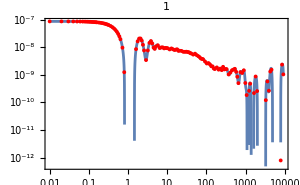
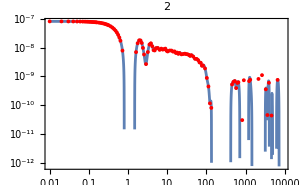
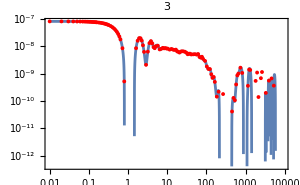
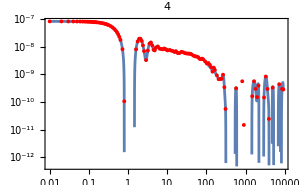
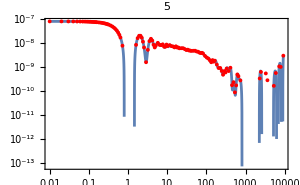
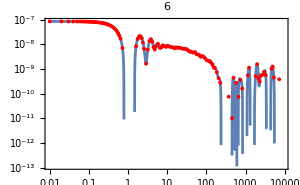
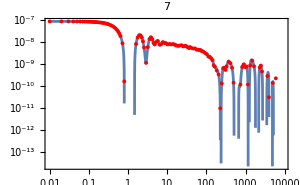
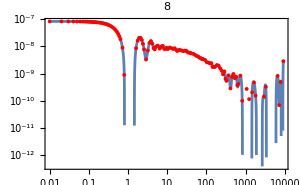

```mathematica
Table[Show[LogLogPlot[sacfInterpSAC3825[[id]][x],{x,0.01,Last[sac3825[[id,2]]]},ImageSize->300,PlotLabel->ToString[id]],ListLogLogPlot[Table[{sac3825[[id,2,i]],sac3825[[id,1,i]]},{i,Length[sac3825[[id,1]]]}],PlotStyle->Red]],{id,Length[sac3825]}]
```

```mathematica
sacCutoff3825={160,130,180,310,740,230,230,410,290,200};
```

```mathematica
viscosity3825=Table[NIntegrate[sacfInterpSAC3825[[i]][x],{x,0,sacCutoff3825[[i]]}],{i,10}]*4096/0.002
```

{1.4924,1.03521,1.29665,1.5482,2.02938,1.37765,1.39587,2.02706,1.88708,1.53534}

```mathematica
Mean[viscosity3825]
```

1.56249

```mathematica
StandardDeviation[viscosity3825]/Sqrt[10]
```

0.103046

### p_0=3.825 ,T=0.005

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00500000_waitingTime10000_idx13.nc"]
```

{/firstValue,/secondValue}

```mathematica
sac3825=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.825/SACtime_N4096_p3.8250_T0.00500000_waitingTime10000_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

```mathematica
sacfInterpSAC3825=Table[Interpolation[Transpose[{Normal[sac3825[[i,2]]],Normal[sac3825[[i,1]]]}],Method->"Spline"],{i,10}];
```

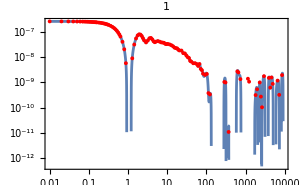
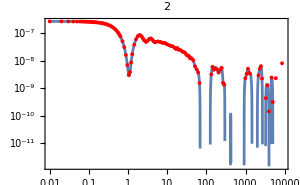
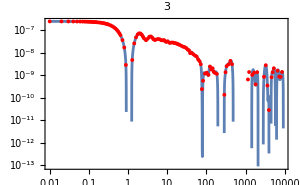
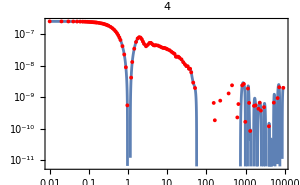
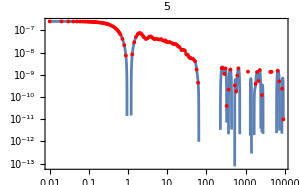
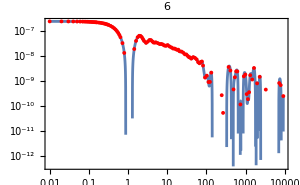
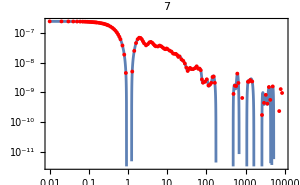
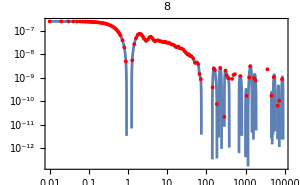

```mathematica
Table[Show[LogLogPlot[sacfInterpSAC3825[[id]][x],{x,0.01,Last[sac3825[[id,2]]]},ImageSize->300,PlotLabel->ToString[id]],ListLogLogPlot[Table[{sac3825[[id,2,i]],sac3825[[id,1,i]]},{i,Length[sac3825[[id,1]]]}],PlotStyle->Red]],{id,Length[sac3825]}]
```

```mathematica
sacCutoff3825={110,67,77,51,61,130,160,72,61,72};
```

```mathematica
viscosity3825=Table[NIntegrate[sacfInterpSAC3825[[i]][x],{x,0,sacCutoff3825[[i]]*1.5}],{i,10}]*4096/0.005
```

{1.0028,1.09162,1.10489,0.804322,0.784453,0.909894,0.983287,0.882681,0.710504,0.731885}

```mathematica
Mean[viscosity3825]
```

0.900633

```mathematica
StandardDeviation[viscosity3825]/Sqrt[10]
```

0.0451259

### p_0=3.75 ,T=0.02

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.750/SACtime_N4096_p3.7500_T0.02000000_waitingTime10000_idx12.nc"]
```

{/firstValue,/secondValue}

```mathematica
sac375=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.750/SACtime_N4096_p3.7500_T0.02000000_waitingTime10000_idx"<>ToString[i]<>".nc","Data"],{i,10,19}];
```

```mathematica
sacfInterpSAC375=Table[Interpolation[Transpose[{Normal[sac375[[i,2]]],Normal[sac375[[i,1]]]}],Method->"Spline"],{i,10}];
```

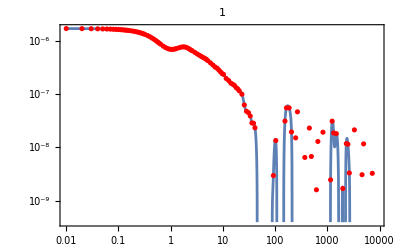
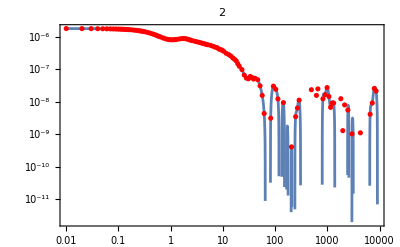
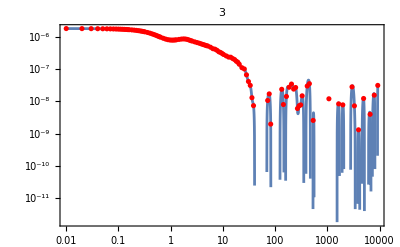
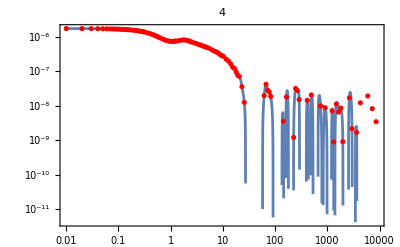
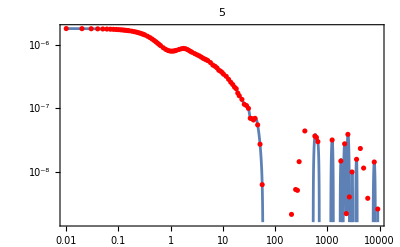
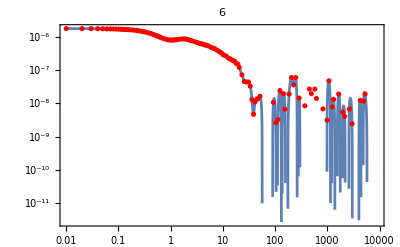
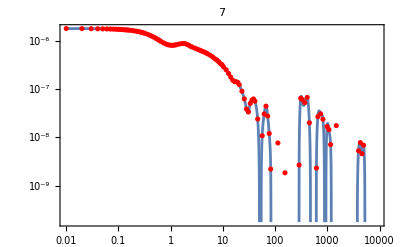
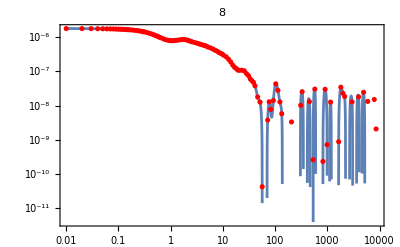

```mathematica
Table[Show[LogLogPlot[sacfInterpSAC375[[id]][x],{x,0.01,Last[sac375[[id,2]]]},ImageSize->400,PlotLabel->ToString[id]],ListLogLogPlot[Table[{sac375[[id,2,i]],sac375[[id,1,i]]},{i,Length[sac375[[id,1]]]}],PlotStyle->Red]],{id,Length[sac375]}]
```

```mathematica
sacCutoff375={41,28,36,26,56,46,28,56,24,36};
```

```mathematica
viscosity375=Table[NIntegrate[sacfInterpSAC375[[i]][x],{x,0,sacCutoff375[[i]]}],{i,10}]*4096/0.02
```

{1.59976,1.98601,1.87886,1.52091,2.36839,1.86661,1.78375,1.97165,1.61707,1.74344}

```mathematica
Mean[viscosity375]
```

1.83365

```mathematica
StandardDeviation[viscosity375]/Sqrt[10]
```

0.077559

## diffusion constant

### p_0=3.75 ,T=0.02

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityAutoCorrelation/velocityAutoCorrelationTime_N4096_p3.7500_T0.02000000_Cell_2_idx10.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

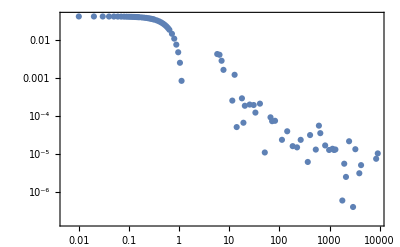

```mathematica
ListLogLogPlot[Table[{test[[2,i]],test[[1,i]]},{i,Length[test[[1]]]}]]
```

```mathematica
vac375=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityAutoCorrelation/velocityAutoCorrelationTime_N4096_p3.7500_T0.02000000_Cell_"<>ToString[i]<>"_idx10.nc","Data"],{i,0,4095}];
```

```mathematica
meanVac375=Table[{vac375[[1,2,i]],Mean[Table[vac375[[cell,1,i]],{cell,Length[vac375]}]]},{i,Length[vac375[[1,2]]]}]
```

{{0.,0.0399954},{0.01,0.0399881},{0.02,0.0399661},{0.03,0.0399295},{0.04,0.0398782},{0.05,0.0398125},{0.06,0.0397322},{0.07,0.0396376},{0.08,0.0395286},{0.09,0.0394055},{0.1,0.0392682},{0.11,0.039117},{0.12,0.0389519},{0.13,0.0387731},{0.14,0.0385808},{0.15,0.0383752},{0.16,0.038153},{0.18,0.0376766},{0.2,0.0371499},{0.22,0.0365746},{0.24,0.0359528},{0.26,0.0352865},{0.28,0.0345779},{0.3,0.0338293},{0.32,0.0330346},{0.36,0.0313617},{0.4,0.0295705},{0.44,0.0276835},{0.48,0.0257237},{0.52,0.0237144},{0.56,0.0216787},{0.6,0.0196394},{0.64,0.0176282},{0.72,0.0137323},{0.8,0.0101375},{0.88,0.00696134},{0.96,0.00428652},{1.04,0.00215826},{1.12,0.000584437},{1.2,-0.000461937},{1.28,-0.000941062},{1.44,-0.0010778},{1.6,-0.000486398},{1.76,0.0000168089},{1.92,-0.000195001},{2.08,-0.00142155},{2.24,-0.00359873},{2.4,-0.00635967},{2.56,-0.00904075},{2.88,-0.0125813},{3.2,-0.0122011},{3.52,-0.00904037},{3.84,-0.00592129},{4.16,-0.004537},{4.48,-0.00425802},{4.8,-0.00334724},{5.12,-0.000851759},{5.76,0.00342743},{6.4,0.00335803},{7.04,0.00270525},{7.68,0.00201907},{8.32,-0.000444649},{8.96,-0.00161102},{9.6,-0.00163844},{10.24,-0.0015634},{11.52,-0.0000427559},{12.8,0.000772798},{14.08,0.000384101},{15.36,-0.000265848},{16.64,-0.000373685},{17.92,-0.0000357218},{19.2,0.000206761},{20.48,0.0000983139},{23.04,-0.0000262906},{25.6,0.0000531},{28.16,-0.0000138063},{30.72,-3.40883×10^-6},{33.28,0.0000321858},{35.84,9.24478×10^-6},{38.4,-7.49914×10^-6},{40.96,-8.11449×10^-6},{46.08,7.9953×10^-6},{51.2,0.0000276717},{56.32,3.19925×10^-6},{61.44,-4.81731×10^-6},{66.56,4.5159×10^-6},{71.68,0.0000186385},{76.8,0.0000131099},{81.92,2.79064×10^-6},{92.16,6.24441×10^-8},{102.4,7.36071×10^-6},{112.64,-3.59335×10^-6},{122.88,3.33997×10^-6},{133.12,-2.55555×10^-6},{143.36,-4.53767×10^-7},{153.6,1.51029×10^-6},{163.84,1.57857×10^-6},{184.32,1.89065×10^-7},{204.8,1.79511×10^-6},{225.28,1.87066×10^-6},{245.76,6.38496×10^-7},{266.24,7.37835×10^-7},{286.72,9.7723×10^-7},{307.2,-3.4075×10^-7},{327.68,-5.9739×10^-7},{368.64,-9.40803×10^-7},{409.6,-6.33618×10^-7},{450.56,-5.26834×10^-7},{491.52,1.63898×10^-6},{532.48,-6.71694×10^-7},{573.44,4.20397×10^-7},{614.4,3.15752×10^-7},{655.36,-8.56466×10^-7},{737.28,-6.01791×10^-7},{819.2,5.2081×10^-7},{901.12,-6.42014×10^-8},{983.04,-1.29965×10^-6},{1064.96,-4.96851×10^-7},{1146.88,-8.78296×10^-7},{1228.8,-1.09184×10^-6},{1310.72,3.746×10^-7},{1474.56,1.32703×10^-6},{1638.4,1.3569×10^-6},{1802.24,3.10936×10^-7},{1966.08,3.83221×10^-7},{2129.92,2.68497×10^-7},{2293.76,8.64197×10^-7},{2457.6,1.25102×10^-7},{2621.44,-1.732×10^-7},{2949.12,4.93454×10^-7},{3276.8,7.31502×10^-7},{3604.48,4.93912×10^-7},{3932.16,-1.64418×10^-7},{4259.84,-1.30673×10^-6},{4587.52,-3.78338×10^-7},{4915.2,-1.27113×10^-7},{5242.88,-4.23594×10^-7},{5898.24,1.72744×10^-7},{6553.6,-2.70027×10^-7},{7208.96,-5.26852×10^-8},{7864.32,-4.14546×10^-7},{8519.68,-1.23976×10^-8},{9175.04,1.29901×10^-6}}

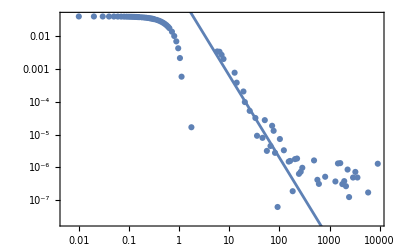

```mathematica
Show[ListLogLogPlot[meanVac375],LogLogPlot[0.2x^(-2.5),{x,1,1000}]]
```

```mathematica
meanVacInterp375=Interpolation[meanVac375,Method->"Spline"]
```

InterpolatingFunction[…]

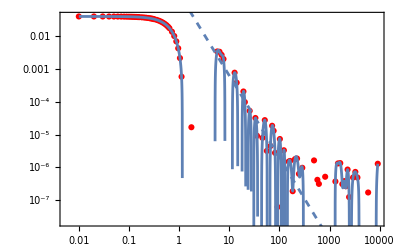

```mathematica
Show[ListLogLogPlot[meanVac375,PlotStyle->Red],LogLogPlot[meanVacInterp375[x],{x,0.01,Last[meanVac375][[1]]}],LogLogPlot[0.2x^(-2.5),{x,1,1000},PlotStyle->Dashed]]
```

```mathematica
diffusionConstant375=NIntegrate[meanVacInterp375[x],{x,0,290}]/2
```

0.0038783

### p_0=3.85 ,T=0.002

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityAutoCorrelation/velocityAutoCorrelationTime_N4096_p3.8500_T0.00200000_Cell_2_idx10.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

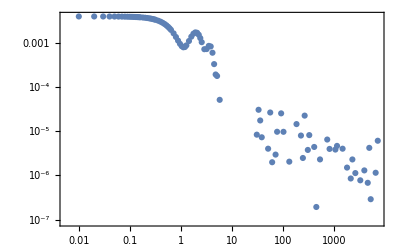

```mathematica
ListLogLogPlot[Table[{test[[2,i]],test[[1,i]]},{i,Length[test[[1]]]}]]
```

```mathematica
vac385=Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/velocityAutoCorrelation/velocityAutoCorrelationTime_N4096_p3.8500_T0.00200000_Cell_"<>ToString[i]<>"_idx10.nc","Data"],{i,0,4095}];
```

```mathematica
meanVac385=Table[{vac385[[1,2,i]],Mean[Table[vac385[[cell,1,i]],{cell,Length[vac385]}]]},{i,Length[vac385[[1,2]]]}]
```

{{0.,0.0039995},{0.01,0.00399885},{0.02,0.00399688},{0.03,0.00399361},{0.04,0.00398904},{0.05,0.00398316},{0.06,0.00397599},{0.07,0.00396754},{0.08,0.0039578},{0.09,0.0039468},{0.1,0.00393453},{0.11,0.00392102},{0.12,0.00390626},{0.13,0.00389029},{0.14,0.00387311},{0.15,0.00385473},{0.16,0.00383489},{0.18,0.00379234},{0.2,0.00374531},{0.22,0.00369399},{0.24,0.00363854},{0.26,0.00357917},{0.28,0.0035161},{0.3,0.00344955},{0.32,0.00337901},{0.36,0.00323083},{0.4,0.00307276},{0.44,0.00290701},{0.48,0.00273586},{0.52,0.0025616},{0.56,0.00238655},{0.6,0.002213},{0.64,0.00204458},{0.72,0.00172508},{0.8,0.00144327},{0.88,0.00121088},{0.96,0.00103594},{1.04,0.000922379},{1.12,0.000870015},{1.2,0.000874733},{1.28,0.000938805},{1.44,0.00114664},{1.6,0.00141061},{1.76,0.00163334},{1.92,0.00174309},{2.08,0.00170983},{2.24,0.00154793},{2.4,0.00130629},{2.56,0.00106148},{2.88,0.000738025},{3.2,0.000737069},{3.52,0.000869487},{3.84,0.000857005},{4.16,0.00063506},{4.48,0.000367087},{4.8,0.000224099},{5.12,0.000212017},{5.76,0.000095073},{6.4,-0.000148053},{7.04,-0.000236997},{7.68,-0.000328031},{8.32,-0.000423009},{8.96,-0.000451669},{9.6,-0.000488926},{10.24,-0.000500481},{11.52,-0.000491404},{12.8,-0.000441536},{14.08,-0.000364994},{15.36,-0.000278221},{16.64,-0.000191452},{17.92,-0.000113964},{19.2,-0.0000508299},{20.48,-8.19034×10^-6},{23.04,0.00003887},{25.6,0.0000390695},{28.16,0.0000183123},{30.72,-3.30235×10^-6},{33.28,-0.0000158886},{35.84,-0.0000183415},{38.4,-0.0000142317},{40.96,-8.3354×10^-6},{46.08,-1.16999×10^-6},{51.2,3.23074×10^-8},{56.32,-1.26303×10^-6},{61.44,-1.54265×10^-6},{66.56,-5.61114×10^-7},{71.68,5.51776×10^-7},{76.8,1.31755×10^-6},{81.92,1.64602×10^-6},{92.16,8.01596×10^-7},{102.4,1.01675×10^-6},{112.64,2.45723×10^-6},{122.88,9.81306×10^-7},{133.12,1.41769×10^-6},{143.36,7.28954×10^-7},{153.6,1.88819×10^-6},{163.84,9.36585×10^-7},{184.32,3.67684×10^-7},{204.8,1.04929×10^-6},{225.28,9.0988×10^-7},{245.76,-2.42466×10^-7},{266.24,6.22917×10^-7},{286.72,4.42821×10^-7},{307.2,6.30819×10^-7},{327.68,1.00881×10^-6},{368.64,5.53707×10^-7},{409.6,1.74792×10^-8},{450.56,1.36554×10^-7},{491.52,3.27549×10^-7},{532.48,-5.76128×10^-8},{573.44,-7.06179×10^-7},{614.4,-4.56709×10^-8},{655.36,1.92438×10^-7},{737.28,-8.76959×10^-8},{819.2,-2.10559×10^-8},{901.12,2.15961×10^-7},{983.04,-2.62575×10^-7},{1064.96,1.51724×10^-7},{1146.88,-6.18645×10^-8},{1228.8,3.38083×10^-7},{1310.72,1.53193×10^-7},{1474.56,2.87468×10^-7},{1638.4,-3.23106×10^-7},{1802.24,-2.18932×10^-7},{1966.08,-3.63326×10^-7},{2129.92,-2.119×10^-7},{2293.76,-8.72671×10^-8},{2457.6,-2.60373×10^-7},{2621.44,-1.23658×10^-7},{2949.12,1.45369×10^-7},{3276.8,-3.53314×10^-8},{3604.48,1.55063×10^-7},{3932.16,-1.92395×10^-7},{4259.84,-8.82128×10^-9},{4587.52,3.0921×10^-9},{4915.2,-5.93492×10^-8},{5242.88,2.87598×10^-8},{5898.24,-1.06668×10^-7},{6553.6,6.22125×10^-8},{7208.96,4.3955×10^-9},{7864.32,-1.59274×10^-8},{8519.68,1.14328×10^-7},{9175.04,2.31226×10^-8}}

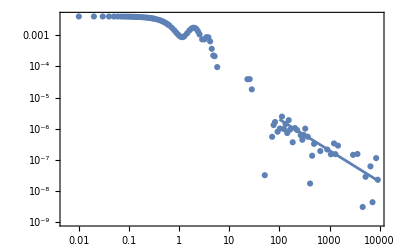

```mathematica
Show[ListLogLogPlot[meanVac385],LogLogPlot[0.0002x^(-1),{x,100,10000}]]
```

```mathematica
meanVacInterp385=Interpolation[meanVac385,Method->"Spline"]
```

InterpolatingFunction[…]

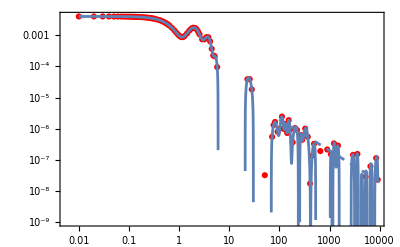

```mathematica
Show[ListLogLogPlot[meanVac385,PlotStyle->Red],LogLogPlot[meanVacInterp385[x],{x,0.01,Last[meanVac385][[1]]}],LogLogPlot[0.0002x^(-1),{x,100,10000},PlotStyle->Dashed]]
```

```mathematica
diffusionConstant375=NIntegrate[meanVacInterp375[x],{x,0,51}]/2
```

0.0011118